```mathematica
park=Import["/Users/thomaslux/Dropbox/Downloads/Paper_[2018-01]_ACMSE/Results/parkinsons_updrs.csv"];
fors= Import["/Users/thomaslux/Dropbox/Downloads/Paper_[2018-01]_ACMSE/Results/forestfires.csv"];
hpci=Import["/Users/thomaslux/Dropbox/Downloads/Paper_[2018-01]_ACMSE/Results/hpc_file_io.csv"];
data = Import["/Users/thomaslux/Dropbox/Downloads/Paper_[2018-01]_ACMSE/Results/ACM_results.csv"];
perf=Import["/Users/thomaslux/Dropbox/Downloads/Paper_[2018-01]_ACMSE/Results/ACM_perf_sample.csv"];
park=park[[1;;4*(Length[park]-1)/50-1,All]];
hpci=hpci[[1;;(Length[hpci]-1)/2+1,All]];

dataNames={"HPC I/O","Forest Fire","Parkinsons"};
algNames={"Max Box Mesh","Iterative Box Mesh", "Voronoi Mesh"};
dataValues[a_,r_:12]:={
namedData[d_]:={
select[row_]:=And[row[[1]]==d,row[[6]]==a];
Select[data,select][[All,r]]
}[[1]];
namedData
}[[1]];

tolValues[a_,r_:12,t_:0]:={
namedData[d_]:={
select[row_]:=And[row[[1]]==d,row[[6]]==a,Abs[row[[2]]-t]<0.01];
Select[data,select][[All,r]]
}[[1]];
namedData
}[[1]];
```

```mathematica
Union[data[[All,1]]]
data[[1,All]]
park[[1,All]]
fors[[1,All]]
hpci[[1,All]]
perf[[1]]
```

{Data,Forest Fire,HPC I/O,Parkinsons}

{Data,Tolerance,Train_Size,Test_Size,Fold_Num,Model_Name,Fit_Time,Eval_Time,Min_Error,Max_Error,Median_Error,Average_Error}

{subject#,age,sex,test_time,motor_UPDRS,total_UPDRS,Jitter(%),Jitter(Abs),Jitter:RAP,Jitter:PPQ5,Jitter:DDP,Shimmer,Shimmer(dB),Shimmer:APQ3,Shimmer:APQ5,Shimmer:APQ11,Shimmer:DDA,NHR,HNR,RPDE,DFA,PPE}

{X,Y,month,day,FFMC,DMC,DC,ISI,temp,RH,wind,rain,area}

{File_Size,Record_Size,Threads,Frequency,Mean_Throughput}

{Data,Model_Name,Tolerance,Tol_Avg_Abs_Error,Num_Samples}

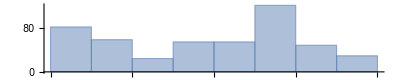

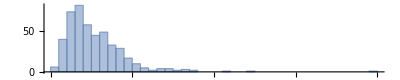

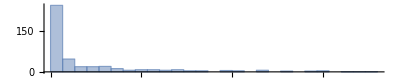

```mathematica
ratio=0.2;
Histogram[{{},park[[All,6]]},PlotRange->Full,AspectRatio->ratio,LabelStyle->{FontFamily->"Times"}]
(*,PlotLabel->StringJoin["Parkinsons Response (",park[[1,6]],")"]]*)
Histogram[{{},park[[All,13]]},PlotRange->Full,AspectRatio->ratio,LabelStyle->{FontFamily->"Times"}]
(*,PlotLabel->StringJoin["Forest Fire Response (",fors[[1,13]],")"]]*)
Histogram[{{},hpci[[All,5]]},PlotRange->Full,AspectRatio->ratio,LabelStyle->{FontFamily->"Times"}]
(*,PlotLabel->StringJoin["HPC I/O Response (",hpci[[1,5]],")"]]*)
```

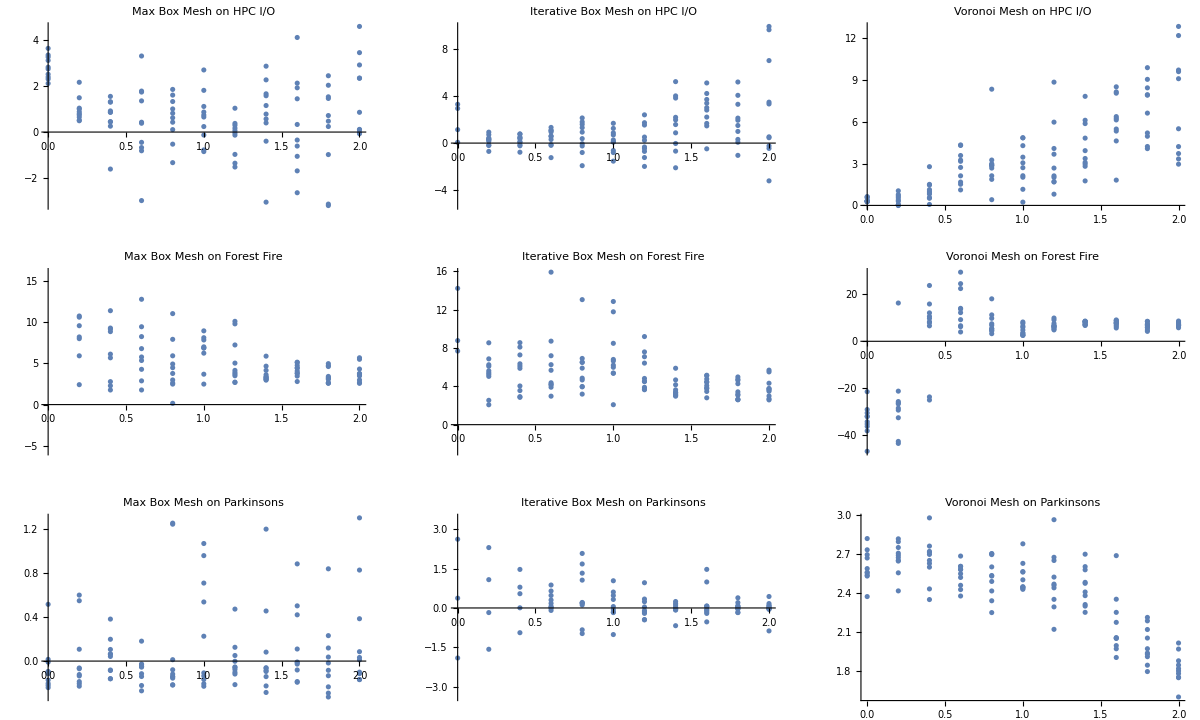
-Graphics-Relative Error ToleranceSigned Relative Error

```mathematica
allPlots={};
For[d=1,d≤Length[dataNames],d=d+1,{
plots={};
For[i=1,i≤Length[algNames],i=i+1,{
error=dataValues[algNames[[i]]][dataNames[[d]]];
tol=dataValues[algNames[[i]],2][dataNames[[d]]];
allData=Transpose[{tol,error}];
AppendTo[plots,ListPlot[allData,PlotLabel->StringJoin[algNames[[i]]," on ",dataNames[[d]]],AspectRatio->.6,LabelStyle->{FontFamily->"Times New Roman"}]]
}];
AppendTo[allPlots,plots];
}];
Labeled[GraphicsGrid[allPlots],{"Relative Error Tolerance","Signed Relative Error"},{Bottom,Left},RotateLabel->True,LabelStyle-> {FontFamily->"Times New Roman"}]
```

```mathematica
plots={};
timeData={};
For[a=1,a≤Length[algNames],a=a+1,{
(* First loop, cycle all the algorithms (individual plots) *)
dataTimes={};
For[d=1,d≤Length[dataNames],d=d+1,{
(* Second loop, cycle all of the data sets (line series) *)
tolTimes={};
For[t=0,t≤2,t=t+1/5,{
(* Third loop, cycle all of the tolerance values (x-values) *)
values=tolValues[algNames[[a]],7,t][dataNames[[d]]];
AppendTo[tolTimes,{t,Mean[values]}];
}];
AppendTo[dataTimes,tolTimes];
}];
AppendTo[timeData,dataTimes];
}];
Dimensions[timeData]
ratio=0.45
AppendTo[plots,ListLinePlot[timeData[[1]],PlotStyle->{Medium,Dashed,Dotted},LabelStyle->{FontFamily->"Times"},AspectRatio->ratio+.05,PlotLabel->algNames[[1]]]];
AppendTo[plots,ListLinePlot[timeData[[2]],PlotStyle->{Medium,Dashed,Dotted},LabelStyle->{FontFamily->"Times"},AspectRatio->ratio,PlotLabel->algNames[[2]],PlotLegends->Placed[dataNames,Above]]];
AppendTo[plots,ListLinePlot[timeData[[3]],PlotStyle->{Medium,Dashed,Dotted},LabelStyle->{FontFamily->"Times"},AspectRatio->ratio+.05,PlotLabel->algNames[[3]]]];
GraphicsRow[plots]
```

{3,3,11,2}

0.45

{HPC I/O,Max Box Mesh,1.2,0.596504,860}

{Forest Fire,Max Box Mesh,1.8,3.517,1030}

{Parkinsons,Max Box Mesh,0.6,0.113788,940}

{HPC I/O,Iterative Box Mesh,0.4,0.418563,860}

{Forest Fire,Iterative Box Mesh,1.8,3.6153,1030}

{Parkinsons,Iterative Box Mesh,1.8,0.121165,940}

{HPC I/O,Voronoi Mesh,0.2,0.381665,860}

{Forest Fire,Voronoi Mesh,1.,4.78312,1030}

{Parkinsons,Voronoi Mesh,2.,1.82384,940}

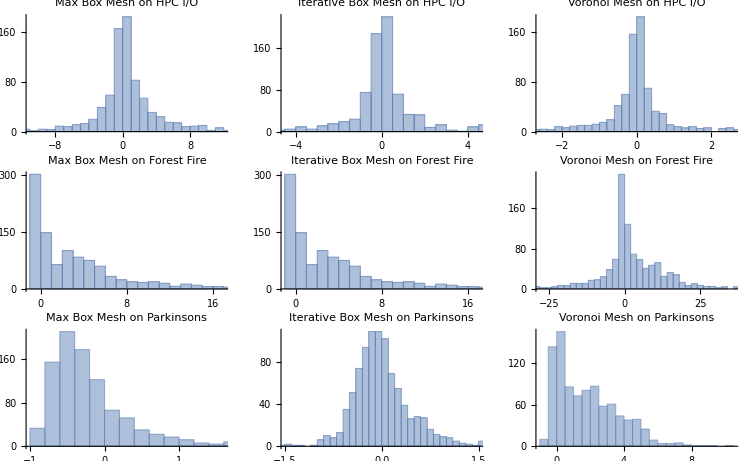

```mathematica
plots={};
For[a=1,a≤Length[algNames],a=a+1,{
row={};
(* First loop, cycle all the algorithms (each column) *)
For[d=1,d≤Length[dataNames],d=d+1,{
(* Second loop, cycle all the data sets (each row) *)
errorRow=perf[[1+(d-1)*3+a]];
Print[errorRow[[1;;5]]];
errors=errorRow[[6;;Length[errorRow]]];
AppendTo[row,Histogram[{{},errors},PlotLabel-> StringJoin[algNames[[a]]," on ",dataNames[[d]]],LabelStyle->{FontFamily->"Times"}]];
}];
AppendTo[plots,row];
}];
GraphicsGrid[Transpose[plots]]
```